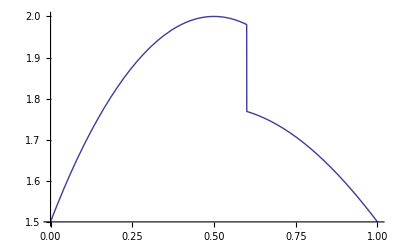

```mathematica
x=3/4;
ys=6/10;
a[y_]:=If[y≤ys,Sin[Pi y],Sin[Pi y]/2]
(**Primal solution**)
u[y_]:=x+Sqrt[x^2+a[y]];
Plot[u[y],{y,0,1},PlotStyle->Thick,AxesLabel->{ξ}]
```

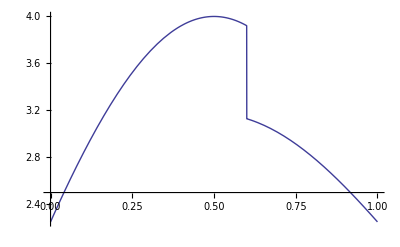

```mathematica
(**Random functional**)
J[y_]:=u[y]^2
Plot[J[y],{y,0,1},PlotStyle->Thick,AxesLabel->{ξ}]
```

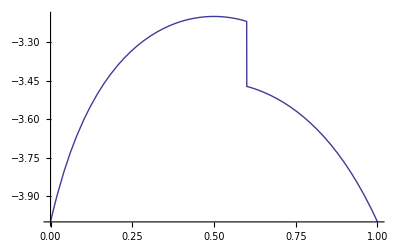

```mathematica
R[u_,y_]:=u^2/2-x u-a[y]/2
(**Adjoint solution**)
v[y_]:=2u[y]/(x-u[y])
Plot[v[y],{y,0,1},PlotStyle->Thick,AxesLabel->{ξ}]
```

```mathematica
(**Mean value of functional**)
mean=N[Integrate[J[y],{y,0,1}],14]
```

3.1988958008986+0. ⅈ